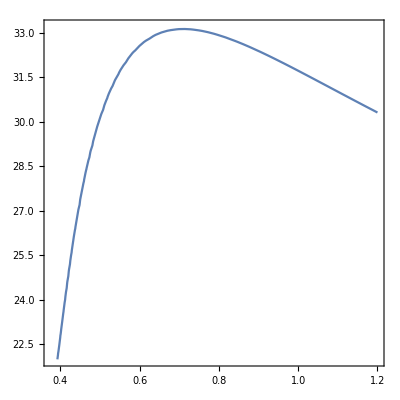

```mathematica
z[x_]:=(0.355*x)/(x-0.355)
no[x_]:=√(2.7359+0.01878/(x^2-0.01822)-0.01354*x^2)
n3[x_]:=1/(√((Cos[x])^2/1.705402312^2+(Sin[x])^2/1.576489296^2))
ContourPlot[n3[y*π/180]/0.355==no[x]/x+no[z[x]]/z[x],{x,0.375,1.2},{y,22,33.2}]
```